```mathematica
Import[new.txt]
```

Import::chtype: First argument new . txt is not a valid file, directory, or URL specification.

$Failed

```mathematica
Import["/home/s1220054/Dissertation/Dissertation/src/new.txt", "CSV"]
```

8,9
8,10
8,11
8,13
9,8
9,9
9,10
9,11
9,12
9,13
9,14
10,8
10,9
10,10
10,11
10,12
10,13
11,10
11,11

```mathematica
data = Import["/home/s1220054/Dissertation/Dissertation/src/new.txt"]
```

8,9
8,10
8,11
8,13
9,8
9,9
9,10
9,11
9,12
9,13
9,14
10,8
10,9
10,10
10,11
10,12
10,13
11,10
11,11

```mathematica
ListPlot[data]
```

ListPlot::lpn: "8,9\n8,10\n8,11\n8,13\n9,8\n9,9\n9,10\n9,11\n9,12\n9,13\n9,14\n10,8\n10,9\n10,10\n10,11\n10,12\n10,13\n11,10\n11,11" is not a list of numbers or pairs of numbers.

ListPlot[8,9
8,10
8,11
8,13
9,8
9,9
9,10
9,11
9,12
9,13
9,14
10,8
10,9
10,10
10,11
10,12
10,13
11,10
11,11]

```mathematica
data = Import["/home/s1220054/Dissertation/Dissertation/src/new.txt"]
```

{8,11}
{9,9}
{9,10}
{9,11}
{9,12}
{9,13}
{9,14}
{9,15}
{10,9}
{10,10}
{10,11}
{10,12}
{10,13}
{11,8}
{11,9}
{11,10}
{11,11}
{11,12}

```mathematica
ListPlot[data]
```

ListPlot::lpn: "{8,11}\n{9,9}\n{9,10}\n{9,11}\n{9,12}\n{9,13}\n{9,14}\n{9,15}\n{10,9}\n{10,10}\n{10,11}\n{10,12}\n{10,13}\n{11,8}\n{11,9}\n{11,10}\n{11,11}\n{11,12}" is not a list of numbers or pairs of numbers.

ListPlot[{8,11}
{9,9}
{9,10}
{9,11}
{9,12}
{9,13}
{9,14}
{9,15}
{10,9}
{10,10}
{10,11}
{10,12}
{10,13}
{11,8}
{11,9}
{11,10}
{11,11}
{11,12}]

```mathematica
data = Import["/home/s1220054/Dissertation/Dissertation/src/new.txt"]
```

(8,8)
(8,9)
(8,10)
(9,7)
(9,8)
(9,9)
(9,10)
(9,11)
(9,12)
(9,13)
(9,14)
(10,7)
(10,8)
(10,9)
(10,10)
(10,11)
(11,9)
(11,10)
(11,11)
(11,12)

```mathematica
ListPlot[data]
```

ListPlot::lpn: "(8,8)\n(8,9)\n(8,10)\n(9,7)\n(9,8)\n(9,9)\n(9,10)\n(9,11)\n(9,12)\n(9,13)\n(9,14)\n(10,7)\n(10,8)\n(10,9)\n(10,10)\n(10,11)\n(11,9)\n(11,10)\n(11,11)\n(11,12)" is not a list of numbers or pairs of numbers.

ListPlot[(8,8)
(8,9)
(8,10)
(9,7)
(9,8)
(9,9)
(9,10)
(9,11)
(9,12)
(9,13)
(9,14)
(10,7)
(10,8)
(10,9)
(10,10)
(10,11)
(11,9)
(11,10)
(11,11)
(11,12)]

```mathematica
data = Import["/home/s1220054/Dissertation/Dissertation/src/new.txt", "CSV"]
```

{{(8,8)},{(8,9)},{(8,10)},{(9,7)},{(9,8)},{(9,9)},{(9,10)},{(9,11)},{(9,12)},{(9,13)},{(9,14)},{(10,7)},{(10,8)},{(10,9)},{(10,10)},{(10,11)},{(11,9)},{(11,10)},{(11,11)},{(11,12)}}

```mathematica
ListPlot[data]
```

-Graphics-

```mathematica
data = Import["/home/s1220054/Dissertation/Dissertation/src/new.txt", "CSV"]
```

{{8,11},{8,12},{9,7},{9,8},{9,9},{9,10},{9,11},{9,12},{10,8},{10,9},{10,10},{10,11},{10,12},{10,13},{10,14},{11,9},{11,10},{11,11},{12,10}}

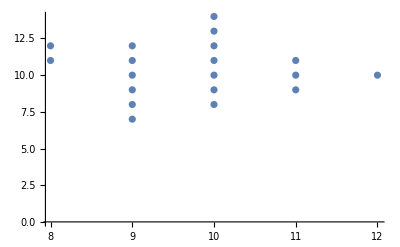

```mathematica
ListPlot[data]
```